```mathematica
f[x_] := (1/2) * ((1+x) * Log[1+x] + (1-x)*Log[1-x]);
```

```mathematica
g := InverseFunction[f];
```

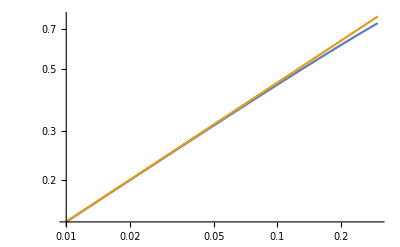

```mathematica
LogLogPlot[{ g[x],Sqrt[2*x]}, {x, .01, 0.3}]
```

```mathematica
num= 10^7;
```

```mathematica
logN = N[Log[num]];
```

```mathematica
logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
times = Import["/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/PaperMax/7_time.txt", "List"];
```

```mathematica
c = Log[num] / times;
```

```mathematica
vals = Map[g, c];
```

```mathematica
takeReal[x_] := Evaluate[Re[x]]
```

```mathematica
realvals = Map[takeReal, vals];
```

```mathematica
Export["/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/PaperMax/7_c1.dat", realvals]
```

/home/jacob/Desktop/Code/extremeDiffusion1D/analysis/PaperMax/7_c1.dat